```mathematica
OS="win";(*or linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\nEDM\\psi-nedm\\Analysis\\mNStar"]];
Print["(DescDir) Rawdata Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\analysis-mirror_neutrons\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",ScrDir="C:\\Users\\tmpra\\Dropbox\\Scratch"];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
];
metaStructure={Real,Word,Real,Real,Real,Real,Real};
metaStructure2={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,"\\","desc.dat"],{Word,Word,Word,Number,Number,Number,Number,Word}];
runst=16;
runend=39;
Print["Runs in the list: ",runNum=descdat[[runst;;runend,4]]];(*11159,11369*)
Print["Size: ",runn=Dimensions[runNum][[1]]];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\psi-nedm\Analysis\mNStar

(DescDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\analysis-mirror_neutrons\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Runs in the list: {13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142}

Size: 24

```mathematica
superdat={};
AccountingForm[TableForm[SetPrecision[superdat,10]]]
Print["Runs in the list: ",runNum2=descdat[[runst;;runend,4]]];
Print["Storage time in the list: ",ts2=descdat[[runst;;runend,7]]];
Print["Size: ",runn2=Dimensions[runNum2][[1]]];
For[runi=1,runi≤runn2,runi++,
metadatascr=ReadList[StringJoin[AscDir,"\\",IntegerString[runNum2[[runi]],10,6],"\\",IntegerString[runNum2[[runi]],10,6],"_Meta5-2.dat"],metaStructure2];
superdat=AppendTo[superdat,{ts2[[runi]],Mean[Table[(PlusMinus[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]]),Sqrt[(metadatascr[[k]][[27]]+metadatascr[[k]][[28]])]])/PlusMinus[(metadatascr[[k]][[30]]),Sqrt[(metadatascr[[k]][[30]])]],{k,3,Dimensions[metadatascr][[1]]}]]+PlusMinus[0,StandardDeviation[(metadatascr[[;;,27]]+metadatascr[[;;,28]])/(metadatascr[[;;,30]])]](**)}];
Print[PlusMinus[0,StandardDeviation[(metadatascr[[;;,27]]+metadatascr[[;;,28]])/(metadatascr[[;;,30]])]](**)]
];
superdat=Sort[superdat,#1[[1]]<#2[[1]]&];
expsuperdat=AccountingForm[TableForm[SetPrecision[superdat,10]]]
```

{}

Runs in the list: {13099,13101,13102,13103,13104,13105,13106,13107,13108,13109,13110,13111,13112,13132,13133,13134,13135,13136,13137,13138,13139,13140,13141,13142}

Storage time in the list: {380,365,350,335,320,305,290,275,260,245,230,215,200,170,155,140,125,110,95,80,65,50,35,180}

Size: 24

0±0.000260786

0±0.000464523

0±0.000259539

0±0.000432537

0±0.000321889

0±0.00226423

0±0.000347509

0±0.000336524

0±0.000375735

0±0.000769117

0±0.000491847

0±0.000694799

0±0.000700045

0±0.000913572

0±0.000717038

0±0.000634645

0±0.000834923

0±0.000911083

0±0.000698243

0±0.000844085

0±0.00111636

0±0.000799289

0±0.00184376

0±0.000605108

35.00000000 | 0.07740000000±0.001800000000
50.00000000 | 0.06917000000±0.0008000000000
65.00000000 | 0.06020000000±0.001100000000
80.00000000 | 0.05393000000±0.0008500000000
95.00000000 | 0.04886000000±0.0007000000000
110.0000000 | 0.04468000000±0.0009100000000
125.0000000 | 0.04059000000±0.0008400000000
140.0000000 | 0.03692000000±0.0006400000000
155.0000000 | 0.03418000000±0.0007200000000
170.0000000 | 0.03044000000±0.0009200000000
180.0000000 | 0.03049000000±0.0006100000000
200.0000000 | 0.02696000000±0.0007000000000
215.0000000 | 0.02498000000±0.0007100000000
230.0000000 | 0.02335000000±0.0004900000000
245.0000000 | 0.02193000000±0.0007700000000
260.0000000 | 0.02028000000±0.0003800000000
275.0000000 | 0.01858000000±0.0003400000000
290.0000000 | 0.01768000000±0.0003500000000
305.0000000 | 0.01640000000±0.002300000000
320.0000000 | 0.01558000000±0.0003200000000
335.0000000 | 0.01492000000±0.0004300000000
350.0000000 | 0.01351000000±0.0002600000000
365.0000000 | 0.01358000000±0.0004700000000
380.0000000 | 0.01191000000±0.0002600000000

```mathematica
superdat2={};
gaps=Table[1,{k,1,runn2}];
Total[gaps]==Dimensions[superdat][[1]]
For[j=1,j≤Dimensions[gaps][[1]],j++,
superdat2=AppendTo[superdat2,Mean[Table[superdat[[j2]],{j2,Total[gaps[[1;;j]]]+1-gaps[[j]],Total[gaps[[1;;j]]]}]]];
];
expsuperdat2=AccountingForm[TableForm[SetPrecision[superdat2,10]]];
superdat3=superdat2+Table[{22.6,PlusMinus[0,.00004]},{k,1,Dimensions[superdat2][[1]]}];
expsuperdat3=AccountingForm[TableForm[SetPrecision[superdat3,10]]]
Export["expsuperdat2-Cu.dat",superdat3]
```

True

57.60000000 | 0.07740000000±0.001800000000
72.60000000 | 0.06917000000±0.0008000000000
87.60000000 | 0.06020000000±0.001100000000
102.6000000 | 0.05393000000±0.0008500000000
117.6000000 | 0.04886000000±0.0007000000000
132.6000000 | 0.04468000000±0.0009100000000
147.6000000 | 0.04059000000±0.0008400000000
162.6000000 | 0.03692000000±0.0006400000000
177.6000000 | 0.03418000000±0.0007200000000
192.6000000 | 0.03044000000±0.0009200000000
202.6000000 | 0.03049000000±0.0006100000000
222.6000000 | 0.02696000000±0.0007000000000
237.6000000 | 0.02498000000±0.0007100000000
252.6000000 | 0.02335000000±0.0004900000000
267.6000000 | 0.02193000000±0.0007700000000
282.6000000 | 0.02028000000±0.0003800000000
297.6000000 | 0.01858000000±0.0003400000000
312.6000000 | 0.01768000000±0.0003500000000
327.6000000 | 0.01640000000±0.002300000000
342.6000000 | 0.01558000000±0.0003200000000
357.6000000 | 0.01492000000±0.0004300000000
372.6000000 | 0.01351000000±0.0002600000000
387.6000000 | 0.01358000000±0.0004700000000
402.6000000 | 0.01191000000±0.0002600000000

expsuperdat2-Cu.dat

FittedModel[0.0743567 ⅇ^(-0.0168726 t)+0.0626634 ⅇ^(-0.00409808 t)]

InterpolatingFunction[…]

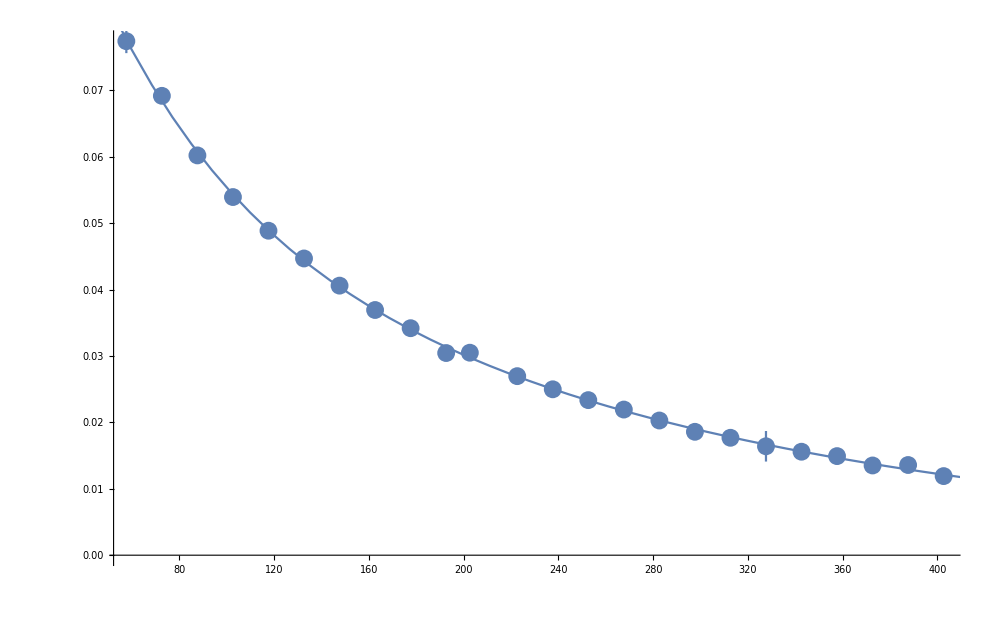

```mathematica
Clear[bb];
ptsuperdat3=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,Dimensions[superdat3][[1]]}];
ftsuperdat3=Table[{superdat3[[k]][[1]],superdat3[[k]][[2]][[1]]},{k,1,Dimensions[superdat3][[1]]}];
Print[nlm0=NonlinearModelFit[ftsuperdat3,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]]
nlm00=Interpolation[ftsuperdat3[[1;;runn2]],InterpolationOrder->1]
rat[x_]:=nlm0[x]/nlm01[x];
rat2[x_]:=nlm00[x]/nlm001[x];
rat3[x_]:=nlm0[x]/ftsuperdat3[[7;;15,2]];
Show[{
EDAListPlot[ptsuperdat3,ImageSize->1000,PlotRange->Full],
Plot[nlm0[xx],{xx,10,420}]
}]
```

```mathematica
Map[nlm0,Table[k,{k,25,225,25}]]
nlm0[57.6]
```

{0.105329,0.0830378,0.0670591,0.0553526,0.0465674,0.0398061,0.0344695,0.0301551,0.0265905}

0.0776229

```mathematica
ptseries1=Table[{superdat3[[k]][[1]],{superdat3[[k]][[2]][[1]],superdat3[[k]][[2]][[2]]}},{k,1,runn2}];
bdptseries=Part[ptseries1,{}];
ptseries2=DeleteCases[ptseries1,Alternatives@@bdptseries];
ftseries2=Transpose[{ptseries2[[;;,1]],ptseries2[[;;,2]][[;;,1]]}];
ptallseries=ptseries2;
ptallseries=Sort[ptallseries,#1[[1]]<#2[[1]]&]
ftallseries=ftseries2;
ftallseries=Sort[ftallseries,#1[[1]]<#2[[1]]&]
errallseries=Table[ptallseries[[k]][[2]][[2]],{k,1,Dimensions[ptallseries][[1]]}];
Print[nlm2=NonlinearModelFit[ftallseries,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
AccountingForm[TableForm[SetPrecision[Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}],4]]];
Export["expsuperdat3-Cu.dat",Table[{ptallseries[[k]][[1]],PlusMinus[ptallseries[[k]][[2]][[1]],ptallseries[[k]][[2]][[2]]]},{k,1,Dimensions[ptallseries][[1]]}]]
nlm0["ParameterTable"]
Print["Sigmas: ",sigmas=(nlm2["FitResiduals"]/errallseries)]
Print["Chi^2/ndf: ",Total[((nlm2["FitResiduals"]/errallseries))^2]/(Dimensions[ftallseries][[1]]-2)]
nlm2["ANOVATable"]
nlm2["ParameterTable"]
Grid[Transpose[{#,nlm2[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[ptallseries,PlotRange->Full,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1000},PlotMarkers->{Red,Medium}],
Plot[{nlm2[xx],nlm2[xx]+nlm2["ParameterErrors"][[1]],nlm2[xx]-nlm2["ParameterErrors"][[1]]},{xx,10,420},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
```

{{57.6,{0.0774,0.0018}},{72.6,{0.06917,0.0008}},{87.6,{0.0602,0.0011}},{102.6,{0.05393,0.00085}},{117.6,{0.04886,0.0007}},{132.6,{0.04468,0.00091}},{147.6,{0.04059,0.00084}},{162.6,{0.03692,0.00064}},{177.6,{0.03418,0.00072}},{192.6,{0.03044,0.00092}},{202.6,{0.03049,0.00061}},{222.6,{0.02696,0.0007}},{237.6,{0.02498,0.00071}},{252.6,{0.02335,0.00049}},{267.6,{0.02193,0.00077}},{282.6,{0.02028,0.00038}},{297.6,{0.01858,0.00034}},{312.6,{0.01768,0.00035}},{327.6,{0.0164,0.0023}},{342.6,{0.01558,0.00032}},{357.6,{0.01492,0.00043}},{372.6,{0.01351,0.00026}},{387.6,{0.01358,0.00047}},{402.6,{0.01191,0.00026}}}

{{57.6,0.0774},{72.6,0.06917},{87.6,0.0602},{102.6,0.05393},{117.6,0.04886},{132.6,0.04468},{147.6,0.04059},{162.6,0.03692},{177.6,0.03418},{192.6,0.03044},{202.6,0.03049},{222.6,0.02696},{237.6,0.02498},{252.6,0.02335},{267.6,0.02193},{282.6,0.02028},{297.6,0.01858},{312.6,0.01768},{327.6,0.0164},{342.6,0.01558},{357.6,0.01492},{372.6,0.01351},{387.6,0.01358},{402.6,0.01191}}

FittedModel[0.0743567 ⅇ^(-0.0168726 t)+0.0626634 ⅇ^(-0.00409808 t)]

expsuperdat3-Cu.dat

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0626634 | 0.00486498 | 12.8805 | 3.85207×10^-11
cc | -0.00409808 | 0.000215127 | -19.0496 | 2.73007×10^-14
dd | 0.0743567 | 0.0028104 | 26.4577 | 4.88047×10^-17
ee | -0.0168726 | 0.00166897 | -10.1096 | 2.63317×10^-9

Sigmas: {-0.123848,0.985686,-0.475051,-0.460258,-0.0905386,0.384445,0.243301,-0.0739106,0.279535,-0.982366,1.20776,0.0773945,-0.0515664,0.094325,0.243428,-0.086435,-1.23001,-0.300295,-0.114049,-0.126324,0.624435,-0.918257,1.43328,-0.804859}

Chi^2/ndf: 0.445387

| DF | SS | MS
Model | 4 | 0.032412 | 0.00810301
Error | 20 | 3.59382×10^-6 | 1.79691×10^-7
Uncorrected Total | 24 | 0.0324156 | 
Corrected Total | 23 | 0.00793426 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0626634 | 0.00486498 | 12.8805 | 3.85207×10^-11
cc | -0.00409808 | 0.000215127 | -19.0496 | 2.73007×10^-14
dd | 0.0743567 | 0.0028104 | 26.4577 | 4.88047×10^-17
ee | -0.0168726 | 0.00166897 | -10.1096 | 2.63317×10^-9

AdjustedRSquared | 0.999867
AIC | -298.66
BIC | -292.769
RSquared | 0.999889

-Graphics-

```mathematica
finpt2=finpt
```

{{57.6,{0.0774,0.000087}},{72.6,{0.067864,0.000087}},{87.6,{0.060225,0.000076}},{102.6,{0.053932,0.000075}},{117.6,{0.048861,0.000072}},{132.6,{0.044329,0.00007}},{147.6,{0.040257,0.000067}},{162.6,{0.036916,0.000069}},{177.6,{0.03418,0.000063}},{192.6,{0.0312315,0.000069}},{202.6,{0.029849,0.000043}},{222.6,{0.026964,0.000061}},{237.6,{0.02498,0.00013}},{252.6,{0.023346,0.000061}},{267.6,{0.021932,0.000062}},{282.6,{0.020281,0.000057}},{297.6,{0.019222,0.000056}},{312.6,{0.017684,0.000054}},{327.6,{0.016402,0.000058}},{342.6,{0.015582,0.000052}},{357.6,{0.01465,0.000054}},{372.6,{0.013514,0.000051}},{387.6,{0.0127,0.000059}},{402.6,{0.011915,0.00004}}}

## Playing

```mathematica
runn2
finpt=Table[{ftallseries[[k]][[1]],{If[k==11||k==23||k==2,ftallseries[[k]][[2]]-2ptallseries[[k]][[2]][[2]],If[k==6||k==7||k==21,ftallseries[[k]][[2]]-0ptallseries[[k]][[2]][[2]],If[k==10,ftallseries[[k]][[2]]+0ptallseries[[k]][[2]][[2]],ftallseries[[k]][[2]]]]],ptallseries[[k]][[2]][[2]]}},{k,1,runn2}];
(***)
tslong={430,480,580,630,680,730,780,830,880,930,980,1030,1080};
longst=ReadList[StringJoin[AscDir,"\\",IntegerString[13145,10,6],"\\",IntegerString[13145,10,6],"_Meta5.edm"],metaStructure2];
For[k=1,k≤Dimensions[tslong][[1]],k++,
finpt=AppendTo[finpt,{tslong[[k]]+22.6,{N[(longst[[k]][[27]]+longst[[k]][[28]])],N[Sqrt[(longst[[k]][[27]]+longst[[k]][[28]])]]}/longst[[k]][[30]]}];
];
errallseries=Table[finpt[[k]][[2]][[2]],{k,1,Dimensions[finpt][[1]]}];
finpt=Table[{finpt[[k]][[1]],{
If[k==26,finpt[[k]][[2]][[1]]+0finpt[[k]][[2]][[2]],
If[k==27||k==28||k==29||k==30||k==31||k==32||k≥33,finpt[[k]][[2]][[1]]-0finpt[[k]][[2]][[2]],
finpt[[k]][[2]][[1]]]],
finpt[[k]][[2]][[2]]}},
{k,1,Dimensions[finpt][[1]]}];
finftpt=Table[{finpt[[k]][[1]],finpt[[k]][[2]][[1]]},{k,1,Dimensions[finpt][[1]]}];
Print[nlm3=NonlinearModelFit[finftpt,(bb Exp[t cc]+dd Exp[t ee]),{{bb,.1},{cc,-.1},{dd,.1},{ee,-.1}},t]];
Export["expsuperdat4-Cu.dat",finpt];
Print["Sigmas: ",(nlm3["FitResiduals"]/errallseries)];
Print["Chi^2/ndf: ",Total[((nlm3["FitResiduals"]/errallseries))^2]/(Dimensions[finpt][[1]]-2)];
nlm3["ANOVATable"]
nlm3["ParameterTable"]
Grid[Transpose[{#,nlm3[#]}&[{"AdjustedRSquared","AIC","BIC","RSquared"}]],Alignment->Left]
Show[{
EDAListPlot[finpt,PlotRange->Full,GridLines->Automatic,Frame->True,FrameStyle->Thickness[.005],PlotStyle->Black,FrameLabel->{"t_Storage (s)","(N_↑+N_↓)/N_Monitor"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->38],LabelStyle->{38,Black,Bold},FrameTicksStyle->Bold,ImageSize->{1400},PlotMarkers->{Red,Medium}],
Plot[{nlm3[xx],nlm3[xx]+nlm2["ParameterErrors"][[1]],nlm3[xx]-nlm2["ParameterErrors"][[1]]},{xx,0,1300},Filling->{2->{3}},FillingStyle->{Opacity[.5],Blue},PlotStyle->{{Blue,Thickness[.005]},None,None}]
}]
(***)
```

24

FittedModel[0.0781624 ⅇ^(-0.0136955 t)+0.0506827 ⅇ^(-0.00356783 t)]

Sigmas: {0.343486,-0.582636,-0.388457,-0.461207,-0.0993403,0.424415,0.360738,0.180598,0.58306,-0.699756,-0.335635,0.496386,0.351374,0.635604,0.545924,0.417437,-0.809138,-0.0435981,-0.0994682,-0.202125,0.433264,-1.4537,-0.980374,-1.75538,0.205469,-2.11467,3.01551,2.61016,0.246273,3.36298,1.31208,-1.17336,2.48307,4.2784,4.42787,4.38153,2.9175}

Chi^2/ndf: 3.34537

| DF | SS | MS
Model | 4 | 0.0323935 | 0.00809837
Error | 33 | 3.31974×10^-6 | 1.00598×10^-7
Uncorrected Total | 37 | 0.0323968 | 
Corrected Total | 36 | 0.0144973 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0506827 | 0.00199602 | 25.3919 | 3.10782×10^-23
cc | -0.00356783 | 0.0000861147 | -41.4312 | 4.90357×10^-30
dd | 0.0781624 | 0.00148857 | 52.5085 | 2.21038×10^-33
ee | -0.0136955 | 0.00051798 | -26.4402 | 8.69067×10^-24

AdjustedRSquared | 0.999885
AIC | -485.147
BIC | -477.093
RSquared | 0.999898

-Graphics-

{{57.6,0.0774},{72.6,0.067864},{87.6,0.060225},{102.6,0.053932},{117.6,0.048861},{132.6,0.044329},{147.6,0.040257},{162.6,0.036916},{177.6,0.03418},{192.6,0.0312315},{202.6,0.029849},{222.6,0.026964},{237.6,0.02498},{252.6,0.023346},{267.6,0.021932},{282.6,0.020281},{297.6,0.019222},{312.6,0.017684},{327.6,0.016402},{342.6,0.015582},{357.6,0.01465},{372.6,0.013514},{387.6,0.0127},{402.6,0.011915},{452.6,0.0102616},{502.6,0.00699381},{552.6,0.00858674},{602.6,0.00615765},{652.6,0.00513385},{702.6,0.00415301},{752.6,0.00365981},{802.6,0.00296326},{852.6,0.00236572},{902.6,0.00213613},{952.6,0.00187387},{1002.6,0.00158884},{1052.6,0.00134111},{1102.6,0.00108551}}

FittedModel[0.0777554 ⅇ^(-0.014005 t)+0.0519109 ⅇ^(-0.00360747 t)]

Sigmas: {6.02043,-2.4728,-5.52631,-5.32772,-1.12067,0.204208,-0.935603,0.959738,5.7508,1.15129,6.97173,4.38169,1.23374,3.53105,5.30839,1.17126,4.92412,-1.84364,-5.36754,-2.74516,-2.93989,-8.69859,-7.87803,-12.7415,-0.18944,-17.3632,5.49446,3.05705,2.77188,0.517569,3.71346,1.74465,-0.660728,3.01566,4.83156,5.00073,4.96991,3.5216}

Chi^2/ndf: 30.1014

| DF | SS | MS
Model | 4 | 0.0325294 | 0.00813234
Error | 34 | 6.92918×10^-6 | 2.03799×10^-7
Uncorrected Total | 38 | 0.0325363 | 
Corrected Total | 37 | 0.0147327 |

| Estimate | Standard Error | t-Statistic | P-Value
bb | 0.0519109 | 0.002753 | 18.8561 | 1.40346×10^-19
cc | -0.00360747 | 0.000116818 | -30.8811 | 1.8498×10^-26
dd | 0.0777554 | 0.00208009 | 37.3808 | 3.35381×10^-29
ee | -0.014005 | 0.000761361 | -18.3946 | 3.02916×10^-19

AdjustedRSquared | 0.999762
AIC | -471.594
BIC | -463.406
RSquared | 0.999787

-Graphics-